```mathematica
$Assumptions = {Vg ∈ Reals, V0 ∈ Reals, κ ∈ Reals, a ∈ Reals, n ∈ Integers, Subscript[k, F] ∈ Reals, q ∈ Reals, q > 0}
```

{Vg∈ℝ,V0∈ℝ,κ∈ℝ,a∈ℝ,n∈ℤ,k_F∈ℝ,q∈ℝ,q>0}

```mathematica
d1F =FullSimplify[ -V0/3(Subscript[k, F]^2/(8 (1 + κ^2)))(8 π + κ^2 (8 π - 3 I a n q (Sqrt[3] Cos[θ] + 3 Sin[θ])))]
```

(V0 (-8 π (1+κ^2)+3 ⅈ a n q κ^2 (√3 Cos[θ]+3 Sin[θ])) k_F^2)/(24 (1+κ^2))

```mathematica
d2F = FullSimplify[(-V0/3) (Subscript[k, F]^2/4) (4 π + (3 Sqrt[3] I a n κ^2 q Cos[θ])/(1 + κ^2))]
```

-1/12 V0 (4 π+(3 ⅈ √3 a n q κ^2 Cos[θ])/(1+κ^2)) k_F^2

```mathematica
d3F = FullSimplify[(-V0/3) (Subscript[k, F]^2/(8 (1 + κ^2))) (8 π + κ^2 (8 π + 3 I a n q (Sqrt[3] Cos[θ] - 3 Sin[θ])))]
```

-(V0 (8 π+κ^2 (8 π+3 ⅈ a n q (√3 Cos[θ]-3 Sin[θ]))) k_F^2)/(24 (1+κ^2))

```mathematica
Series[d3F, {q, 0, 1}]
```

-1/3 π V0 k_F^2-(ⅈ a n V0 κ^2 (√3 Cos[θ]-3 Sin[θ]) k_F^2 q)/(8 (1+κ^2))+O[q]^2

```mathematica
Δ  = -1/3 π V0 Subscript[k, F]^2
```

-1/3 π V0 k_F^2

```mathematica
d1Fp = (ⅈ a n V0 κ^2 (√3 Cos[θ]+3 Sin[θ]) Subscript[k, F]^2 q)/(8 (1+κ^2))
```

(ⅈ a n q V0 κ^2 (√3 Cos[θ]+3 Sin[θ]) k_F^2)/(8 (1+κ^2))

```mathematica
d2Fp = -(ⅈ √3 a n V0 κ^2 Cos[θ] Subscript[k, F]^2 q)/(4 (1+κ^2))
```

-(ⅈ √3 a n q V0 κ^2 Cos[θ] k_F^2)/(4 (1+κ^2))

```mathematica
d3Fp = -(ⅈ a n V0 κ^2 (√3 Cos[θ]-3 Sin[θ]) Subscript[k, F]^2 q)/(8 (1+κ^2))
```

-(ⅈ a n q V0 κ^2 (√3 Cos[θ]-3 Sin[θ]) k_F^2)/(8 (1+κ^2))

```mathematica
Hp = {{0, d1Fp, Conjugate[d3Fp]}, {Conjugate[d1Fp], 0, d2Fp}, {d3Fp, Conjugate[d2Fp] ,0}}
```

{{0,(ⅈ a n q V0 κ^2 (√3 Cos[θ]+3 Sin[θ]) k_F^2)/(8 (1+κ^2)),1/(8 (1+Conjugate[κ]^2))ⅈ Conjugate[a n q V0] Conjugate[κ]^2 (√3 Conjugate[Cos[θ]]-3 Conjugate[Sin[θ]]) Conjugate[k_F]^2},{-1/(8 (1+Conjugate[κ]^2))ⅈ Conjugate[a n q V0] Conjugate[κ]^2 (√3 Conjugate[Cos[θ]]+3 Conjugate[Sin[θ]]) Conjugate[k_F]^2,0,-(ⅈ √3 a n q V0 κ^2 Cos[θ] k_F^2)/(4 (1+κ^2))},{-(ⅈ a n q V0 κ^2 (√3 Cos[θ]-3 Sin[θ]) k_F^2)/(8 (1+κ^2)),(ⅈ √3 Conjugate[κ]^2 Conjugate[a n q V0 Cos[θ]] Conjugate[k_F]^2)/(4 (1+Conjugate[κ]^2)),0}}

```mathematica
ω = Exp[I 2 π/3]
```

ⅇ^((2 ⅈ π)/3)

```mathematica
v0 = 1/Sqrt[3]{1, ω^0, ω^(2 * 0)}
v1 = 1/Sqrt[3]{1, ω^1, ω^(2 * 1)}
v2 = 1/Sqrt[3]{1, ω^2, ω^(2 * 2)}
```

{1/(√3),1/(√3),1/(√3)}

{1/(√3),ⅇ^((2 ⅈ π)/3)/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3)}

{1/(√3),ⅇ^(-(2 ⅈ π)/3)/(√3),ⅇ^((2 ⅈ π)/3)/(√3)}

```mathematica
E0 = 0 + Conjugate[Δ] * ω^0 + Δ * ω^(2 * 0)
E1 = 0 + Conjugate[Δ] * ω^1 + Δ * ω^(2 * 1)
E2 = 0 + Conjugate[Δ] * ω^2 + Δ * ω^(2 * 2)
```

-1/3 π Conjugate[V0] Conjugate[k_F]^2-1/3 π V0 k_F^2

-1/3 ⅇ^((2 ⅈ π)/3) π Conjugate[V0] Conjugate[k_F]^2-1/3 ⅇ^(-(2 ⅈ π)/3) π V0 k_F^2

-1/3 ⅇ^(-(2 ⅈ π)/3) π Conjugate[V0] Conjugate[k_F]^2-1/3 ⅇ^((2 ⅈ π)/3) π V0 k_F^2

```mathematica
v0p= FullSimplify[(Conjugate[v1].Hp.v0)/(E0 - E1)*v1 + (Conjugate[v2].Hp.v0)/(E0 - E2)*v2 + v0 ]
```

{(24-(ⅈ a n q κ^2 (5 √3 Cos[θ]+√3 Cos[Conjugate[θ]]+3 Sin[θ]-3 Sin[Conjugate[θ]]))/(π (1+κ^2)))/(24 √3),(24+(ⅈ a n q κ^2 (4 √3 Cos[θ]+5 √3 Cos[Conjugate[θ]]+6 Sin[θ]+3 Sin[Conjugate[θ]]))/(π (1+κ^2)))/(24 √3),(24+(ⅈ a n q κ^2 (√3 Cos[θ]-4 √3 Cos[Conjugate[θ]]-3 (Sin[θ]+2 Sin[Conjugate[θ]])))/(π (1+κ^2)))/(24 √3)}

```mathematica
G1 = (2π)/a{1, -1/Sqrt[3]}
G2 = (2π)/a{0, 2/Sqrt[3]}
G3 = -G1 - G2
Subscript[κ, 1]=2/3 G1 + 1/3 G2
Subscript[κ, 3]=Subscript[κ, 1]-G1
Subscript[κ, 5]=Subscript[κ, 1]+G3
κ = Norm[Subscript[κ, 1]]
Subscript[k, F] = 10^-4 κ
```

{(2 π)/a,-(2 π)/(√3 a)}

{0,(4 π)/(√3 a)}

{-(2 π)/a,-(2 π)/(√3 a)}

{(4 π)/(3 a),0}

{-(2 π)/(3 a),(2 π)/(√3 a)}

{-(2 π)/(3 a),-(2 π)/(√3 a)}

(4 π)/(3 Abs[a])

π/(7500 Abs[a])

```mathematica
θ = 0
```

0

```mathematica
v0p1 = Normalize[v0p]
```

{(24-(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √((Abs[24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24-(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728)),(24+(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √((Abs[24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24-(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728)),(24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √((Abs[24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24-(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728))}

```mathematica
θ =2 π/3
```

(2 π)/3

```mathematica
v0p3 = Normalize[v0p]
```

{(24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √(1/3+(Abs[24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728)),1/(√3 √(1/3+(Abs[24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728)),(24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √(1/3+(Abs[24-(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728))}

```mathematica
θ = 4 π/3
```

(4 π)/3

```mathematica
v0p5 = Normalize[v0p]
```

{(24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √((Abs[24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24-(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728)),(24-(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √((Abs[24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24-(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728)),(24+(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2))/(24 √3 √((Abs[24+(16 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24+(32 ⅈ a n π q)/(√3 (1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728+(Abs[24-(16 ⅈ √3 a n π q)/((1+(16 π^2)/(9 Abs[a]^2)) Abs[a]^2)]^2)/1728))}

```mathematica
PO = FullSimplify[((Conjugate[v0p1].v0p3) * (Conjugate[v0p3].v0p5) * (Conjugate[v0p5].v0p1))]
```

(((9 a^2+16 π^2)^2-52 π^2 Abs[a n q]^2) ((9 a^2+16 π^2)^2-4 π^2 Abs[a n q]^2)^2)/((9 a^2+16 π^2)^6 (1+8 π^2 Re[(a n q)/(9 a^2+16 π^2)]^2) (1+56 π^2 Re[(a n q)/(9 a^2+16 π^2)]^2)^2)

```mathematica
q = Subscript[k, F]
a = 1
```

π/(7500 Abs[a])

1

```mathematica
FullSimplify[PO]
```

((-(13 n^2 π^4)/14062500+(9+16 π^2)^2) (-(n^2 π^4)/14062500+(9+16 π^2)^2)^2)/((9+16 π^2)^6 (1+(n^2 π^4)/(7031250 (9+16 π^2)^2)) (1+(7 n^2 π^4)/(7031250 (9+16 π^2)^2))^2)

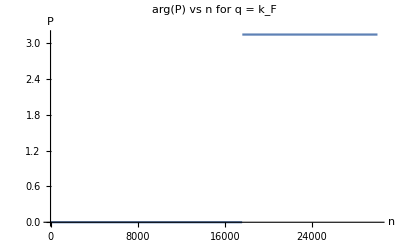

```mathematica
Plot[Arg[PO],{n,1,30000}, AxesLabel->{"n", "P"}, PlotLabel->"arg(P) vs n for q = k_F"]
```

```mathematica
Clear[q, n]
```

```mathematica
n = 30000
```

30000

```mathematica
FullSimplify[PO]
```

(((9+16 π^2)^2-46800000000 π^2 q^2) ((9+16 π^2)^2-3600000000 π^2 q^2)^2)/(((9+16 π^2)^2+7200000000 π^2 q^2) ((9+16 π^2)^2+50400000000 π^2 q^2)^2)

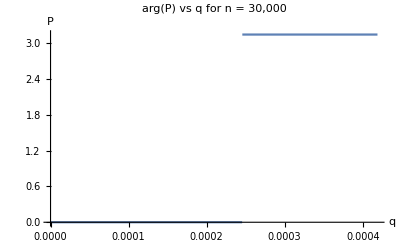

```mathematica
Plot[Arg[PO],{q,0, Subscript[k, F]}, AxesLabel->{"q", "P"}, PlotLabel->"arg(P) vs q for n = 30,000"]
```

# With Kinetic

```mathematica
Clear[θ, n, q]
```

```mathematica
Hk = {{v * q * Cos[θ], 0, 0}, {0, v * q * Cos[θ - 2 π/3], 0}, {0, 0, v * q * Cos[θ - 4 π/3]}}
```

{{q v Cos[θ],0,0},{0,-q v Sin[π/6-θ],0},{0,0,-q v Sin[π/6+θ]}}

```mathematica
kvecs = Eigenvectors[Hk]
kvals = Eigenvalues[Hk]
```

{{1,0,0},{0,1,0},{0,0,1}}

{q v Cos[θ],-q v Sin[π/6-θ],-q v Sin[π/6+θ]}

```mathematica
v0pq = FullSimplify[(Conjugate[v1].(Hp + Hk).v0)/(E0 - E1)*v1 + (Conjugate[v2].(Hp + Hk).v0)/(E0 - E2)*v2 + v0 ]
```

{(3-(168750000 q v Cos[θ])/(π^3 V0)-(2 ⅈ n π q (5 √3 Cos[θ]+√3 Cos[Conjugate[θ]]+3 Sin[θ]-3 Sin[Conjugate[θ]]))/(9+16 π^2))/(3 √3),1/(√3)+(8 ⅈ n π q Cos[θ])/(27+48 π^2)+(9375000 q v (√3 Cos[θ]-3 Sin[θ]))/(π^3 V0)+(2 ⅈ n π q (5 Cos[Conjugate[θ]]+√3 (2 Sin[θ]+Sin[Conjugate[θ]])))/(27+48 π^2),1/(√3)+(9375000 q v (√3 Cos[θ]+3 Sin[θ]))/(π^3 V0)+(2 ⅈ n π q (Cos[θ]-4 Cos[Conjugate[θ]]-√3 (Sin[θ]+2 Sin[Conjugate[θ]])))/(27+48 π^2)}

```mathematica
v = 10^6
```

1000000

```mathematica
θ = 0
```

0

```mathematica
v0pq1 = Normalize[v0pq]
```

{(3-(12 ⅈ √3 n π q)/(9+16 π^2)-(168750000000000 q)/(π^3 V0))/(3 √3 √(1/27 Abs[3-(12 ⅈ √3 n π q)/(9+16 π^2)-(168750000000000 q)/(π^3 V0)]^2+Abs[1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)+(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2)),(1/(√3)+(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0))/(√(1/27 Abs[3-(12 ⅈ √3 n π q)/(9+16 π^2)-(168750000000000 q)/(π^3 V0)]^2+Abs[1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)+(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2)),(1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0))/(√(1/27 Abs[3-(12 ⅈ √3 n π q)/(9+16 π^2)-(168750000000000 q)/(π^3 V0)]^2+Abs[1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)+(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2))}

```mathematica
θ = 2 π/3
```

(2 π)/3

```mathematica
v0pq3 = Normalize[v0pq]
```

{(3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0))/(3 √3 √(1/27 Abs[3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0)]^2+Abs[1/(√3)-(18750000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2)),(1/(√3)-(18750000000000 √3 q)/(π^3 V0))/(√(1/27 Abs[3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0)]^2+Abs[1/(√3)-(18750000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2)),(1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0))/(√(1/27 Abs[3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0)]^2+Abs[1/(√3)-(18750000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)-(6 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2))}

```mathematica
θ = 4 π/3
```

(4 π)/3

```mathematica
v0pq5= Normalize[v0pq]
```

{(3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0))/(3 √3 √(1/27 Abs[3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0)]^2+Abs[1/(√3)+(12 ⅈ n π q)/(27+48 π^2)-(18750000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)-(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2)),(1/(√3)-(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0))/(√(1/27 Abs[3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0)]^2+Abs[1/(√3)+(12 ⅈ n π q)/(27+48 π^2)-(18750000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)-(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2)),(1/(√3)+(12 ⅈ n π q)/(27+48 π^2)-(18750000000000 √3 q)/(π^3 V0))/(√(1/27 Abs[3+(6 ⅈ √3 n π q)/(9+16 π^2)+(84375000000000 q)/(π^3 V0)]^2+Abs[1/(√3)+(12 ⅈ n π q)/(27+48 π^2)-(18750000000000 √3 q)/(π^3 V0)]^2+Abs[1/(√3)-(18 ⅈ n π q)/(27+48 π^2)+(9375000000000 √3 q)/(π^3 V0)]^2))}

```mathematica
POq = FullSimplify[((Conjugate[v0pq1].v0pq3) * (Conjugate[v0pq3].v0pq5) * (Conjugate[v0pq5].v0pq1))]
```

((-791015625000000000000000000 (9+16 π^2)^2 q^2+112500000000000 ⅈ √3 n π^4 (9+16 π^2) q^2 V0+π^6 ((9+16 π^2)^2-52 n^2 π^2 q^2) V0^2) (-791015625000000000000000000 (9+16 π^2)^2 q^2+112500000000000 ⅈ √3 n π^4 (9+16 π^2) q^2 V0+π^6 (9+16 π^2-2 n π q) (9+2 π (8 π+n q)) V0^2)^2)/((π^6 (9+16 π^2)^2 V0^2+8 q^2 (197753906250000000000000000 (9+16 π^2)^2+n^2 π^8 V0^2)) (1582031250000000000000000000 (9+16 π^2)^2 q^2+π^4 V0^2 (π^2 (9+16 π^2)^2+8 n q^2 (7 n π^4-28125000000000 √3 (9+16 π^2) Im[1/V0]))) (1582031250000000000000000000 (9+16 π^2)^2 q^2+π^4 V0^2 (π^2 (9+16 π^2)^2+8 n q^2 (7 n π^4+28125000000000 √3 (9+16 π^2) Im[1/V0]))))

```mathematica
q = Subscript[k, F]
a = 1
V0 = 1
```

π/7500

1

1

```mathematica
FullSimplify[PO]
```

((-(13 n^2 π^4)/14062500+(9+16 π^2)^2) (-(n^2 π^4)/14062500+(9+16 π^2)^2)^2)/((9+16 π^2)^6 (1+(n^2 π^4)/(7031250 (9+16 π^2)^2)) (1+(7 n^2 π^4)/(7031250 (9+16 π^2)^2))^2)

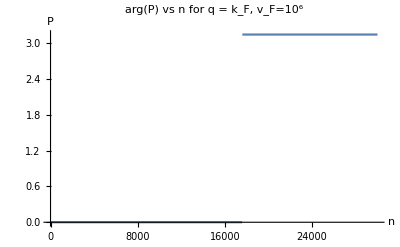

```mathematica
Plot[Arg[PO],{n,1,30000}, AxesLabel->{"n", "P"}, PlotLabel->"arg(P) vs n for q = k_F, v_F=10^6"]
```